%%%GR-LIMIT:

```mathematica
n=2
```

2

```mathematica
%%Define yeh and Translate y to xi
```

```mathematica
yeh=2
```

2

```mathematica
y=2/(1-xi)
```

2/(1-xi)

```mathematica
%%%calculatoing the mass functions in terms of xi:
```

```mathematica
M[xi]=1
```

1

```mathematica
M'[xi]=0
```

0

```mathematica
M''[xi]=0
```

0

```mathematica
Derivative[3][M][xi]=0
```

0

```mathematica
Derivative[4][M][xi]=0
```

0

```mathematica
%%%Potential: Tiene que cambiar a axial!!! Todavia falta!!!
```

```mathematica
V[xi_]=
FullSimplify[3  xi (1-xi)^2/2 - 3 xi  (1-xi)^3/4]
```

3/4 (-1+xi)^2 xi (1+xi)

```mathematica
%%% xi:[0,1]
```

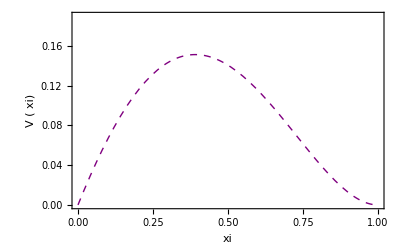

```mathematica
Plot[V[xi],{xi,0,1},Frame->True,PlotRange->{0,0.19},FrameLabel->{Style[" xi ",Large,Black],Style[" V ( xi) ",Large,Black]}, PlotStyle->{{Purple, Thick, Dashed},{Purple, Thick,Dashed}}, FrameLabel->Automatic]
```

```mathematica
F1[xi_]=FullSimplify[-(2/(1-xi))(1 -((1-xi)/yeh)(M[xi]-M'[xi] yeh/(1-xi))/(1- 2(1-xi)M[xi]/yeh))]
```

2/(-1+xi)+1/xi

```mathematica
F2[xi_]=FullSimplify[- ω^2 /(1-2 (1-xi) M[xi]/yeh)^2  (yeh^2/(1-xi)^4)]
```

-(4 ω^2)/((-1+xi)^4 xi^2)

```mathematica
F3[xi_]=FullSimplify[-V[xi] /(1-2 (1-xi) M[xi]/yeh)^2  (yeh^2/(1-xi)^4)]
```

-(3 (1+xi))/((-1+xi)^2 xi)

```mathematica
%%%CAMBIAR ω a -I ω
```

```mathematica
Zx[xi_]=(1-xi)^(-2ω) xi^(-2 ω) ⅇ^(ω yeh/(1-xi))
```

ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-2 ω)

```mathematica
Z[xi_]:=Zx[xi] PP[xi]
```

```mathematica
ZDy1[xi_]:=D[Z[xi],xi]
```

```mathematica
ZDy2[xi_]:=D[ZDy1[xi],xi]
```

```mathematica
EQA[xi_]:= ZDy2[xi]+ F1[xi] ZDy1[xi] +( F2[xi] + F3[xi]) Z[xi]
```

```mathematica
cc0= Coefficient[EQA[xi], PP''[xi]]
```

ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-2 ω)

```mathematica
EQa[xi_]:=EQA[xi]/cc0
```

```mathematica
Coefficient[EQa[xi], PP''[xi]]
```

1

```mathematica
Coefficient[EQa[xi], PP'[xi]]
```

ⅇ^(-(2 ω)/(1-xi)) (1-xi)^(2 ω) xi^(2 ω) (ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-1-2 ω)+(2 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-2 ω))/(-1+xi)-4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-1-2 ω) ω+4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω+4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-1-2 ω) xi^(-2 ω) ω)

```mathematica
Coefficient[EQa[xi], PP[xi]]
```

ⅇ^(-(2 ω)/(1-xi)) (1-xi)^(2 ω) xi^(2 ω) (-(3 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-1-2 ω))/(-1+xi)^2-(3 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-2 ω))/(-1+xi)^2+2 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2-2 ω) xi^(-1-2 ω) ω+2 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-1-2 ω) xi^(-1-2 ω) ω-(4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-1-2 ω) ω)/(-1+xi)+4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-3-2 ω) xi^(-2 ω) ω+2 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω+(4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω)/(-1+xi)+(4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-1-2 ω) xi^(-2 ω) ω)/(-1+xi)+4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-2-2 ω) ω^2-(4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2 ω) xi^(-2-2 ω) ω^2)/(-1+xi)^4-8 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2-2 ω) xi^(-1-2 ω) ω^2-8 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-1-2 ω) xi^(-1-2 ω) ω^2+4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-4-2 ω) xi^(-2 ω) ω^2+8 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-3-2 ω) xi^(-2 ω) ω^2+4 ⅇ^((2 ω)/(1-xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω^2)

λ0[y_,om_]:=FullSimplify[Coefficient[EQa[y], PP'[y]]],

```mathematica
FullSimplify[Coefficient[EQa[xi], PP'[xi]]]
```

(1-4 ω+xi (-4+3 xi-8 (-2+xi) ω))/((-1+xi)^2 xi)

```mathematica
TAKE AN EXTRA MINUS SIGN IN ORDER TO RELATE TO TEH AIM EAUATIONS!
```

```mathematica
λ0[xi_,ω_]:=-((1-4 ω+xi (-4+3 xi-8 (-2+xi) ω))/((-1+xi)^2 xi))
```

```mathematica
λ0[xi,ω]
```

-(1-4 ω+xi (-4+3 xi-8 (-2+xi) ω))/((-1+xi)^2 xi)

s0[y_,  om_] := FullSimplify[Coefficient[EQa[y], PP[y]]]

```mathematica
Simplify[Coefficient[EQa[xi], PP[xi]]]
```

(-3+8 ω-32 ω^2+xi (-3-8 ω+16 ω^2))/((-1+xi)^2 xi)

```mathematica
s0[xi_,ω_]:=-((-3+8 ω-32 ω^2+xi (-3-8 ω+16 ω^2))/((-1+xi)^2 xi))
```

```mathematica
s0[xi,ω]
```

-(-3+8 ω-32 ω^2+xi (-3-8 ω+16 ω^2))/((-1+xi)^2 xi)

```mathematica
λ0[xi, ω]
```

```mathematica
-(1-4 ω+xi (-4+3 xi-8 (-2+xi) ω))/((-1+xi)^2 xi)
```